```mathematica
Quit
```

## Efficiency

## Introduction

### Reference

```mathematica
https://mathematica.stackexchange.com/
```

```mathematica
https://community.wolfram.com/
```

```mathematica
Mathematica® programming:an advanced introduction(https://www.mathprogramming-intro.org/)
```

```mathematica
https://www.zhihu.com/
```

Of course the documentation of Mathematica is the most important. The most important thing is writing code instead of reading books.

### Some general principles

```mathematica
ClearAll[x,y,$y]
```

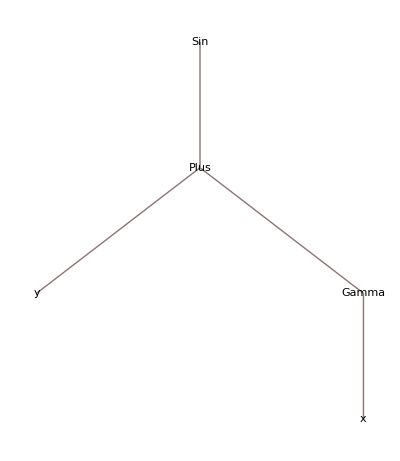

```mathematica
Sin[Gamma[x]+y]//TreeForm
```

```mathematica
$y=2Pi;
```

```mathematica
Sin[Gamma[x]+$y]//Trace
```

{{{$y,2 π},Gamma[x]+2 π,2 π+Gamma[x]},Sin[2 π+Gamma[x]],Sin[Gamma[x]]}

To see how the substitution happens, for example

```mathematica
ClearAttributes[DeleteDuplicatesBy,ReadProtected];
```

```mathematica
??DeleteDuplicatesBy
```

Or the equivalent way:

```mathematica
<<GeneralUtilities`
```

```mathematica
PrintDefinitions@DeleteDuplicatesBy
```

“DeleteDuplicatesBy” is a function in Wolfram Language, but the majorities are written in C:

```mathematica
PrintDefinitions@Gamma
```

## Example on efficiency tuning

Given a array of integers, double all the even number inside the table.

```mathematica
array=RandomInteger[100,10^4];
```

### Without Compile

Some stupid implementation:

```mathematica
(arrayAppend={};
For[i=1,i<=Length@array,i++,If[EvenQ@array[[i]],AppendTo[arrayAppend,2*array[[i]]],AppendTo[arrayAppend,array[[i]]]]];)//RepeatedTiming
```

{0.0983958,Null}

```mathematica
(arrayFor=array;
For[i=1,i<=Length@array,i++,If[EvenQ@arrayFor[[i]],arrayFor[[i]]*=2]];)//RepeatedTiming
```

{0.00989038,Null}

```mathematica
(arrayDo=array;
Do[If[EvenQ@arrayDo[[i]],arrayDo[[i]]*=2],{i,Length@array}];)//RepeatedTiming
```

{0.00667786,Null}

ReplaceAll:

```mathematica
arrayRule=array/.x_?EvenQ->2x;//RepeatedTiming
```

{0.00291413,Null}

Map:

```mathematica
arrayMap=If[EvenQ@#,2#,#]&/@array;//RepeatedTiming
```

{0.000349846,Null}

Table:

```mathematica
arrayTable=Table[If[EvenQ@x,2x,x],{x,array}];//RepeatedTiming
```

{0.00032517,Null}

```mathematica
ParallelTable[If[EvenQ@x,2x,x],{x,array}];//RepeatedTiming
```

{0.0207643,Null}

Actually Map and Table secretly used Compile that we will discuss later!

Some magic:

```mathematica
arrayMod=Mod[array,2,1]*array;//RepeatedTiming
```

{0.0000247731,Null}

```mathematica
arrayAppend==arrayFor==arrayDo==arrayRule==arrayMap==arrayTable==arrayMod
```

True

```mathematica
Developer`PackedArrayQ/@{arrayAppend,arrayFor,arrayDo,arrayRule,arrayMap,arrayTable,arrayMod}
```

{False,True,True,False,True,True,True}

### Compilers

```mathematica
ClearAll@array
```

```mathematica
Needs["CompiledFunctionTools`"]
Compiler`$CCompilerOptions={"SystemCompileOptions"->"-O3 -mcpu=apple-m1"};
```

```mathematica
$CompileListable=Compile[{{x,_Integer}},If[EvenQ@x,2x,x],RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
$CompileListable=Compile[{{x,_Integer}},If[EvenQ@x,2x,x],RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
$CompileListableC=Compile[{{x,_Integer}},If[EvenQ@x,2x,x],CompilationTarget->"C",RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
$CompileListable1=Compile[{{x,_Integer}},If[EvenQ@x,2x,x](*,RuntimeAttributes->{Listable}*),RuntimeOptions->"Speed"];
$CompileListableC1=Compile[{{x,_Integer}},If[EvenQ@x,2x,x],CompilationTarget->"C",(*RuntimeAttributes->{Listable},*)RuntimeOptions->"Speed"];
```

```mathematica
$CompileListable[array];//RepeatedTiming
```

{0.398844,Null}

```mathematica
$CompileListable1/@array;//RepeatedTiming
```

{0.306296,Null}

```mathematica
$CompileListableC[array];//RepeatedTiming
```

{0.227854,Null}

```mathematica
$CompileListableC1/@array;//RepeatedTiming
```

{0.000192376,Null}

```mathematica
$CompileListableTable=Compile[{{x,_Integer,1}},Table[If[EvenQ@i,2i,i],{i,x}],CompilationTarget->"C",RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
$CompileListableTable[array];//RepeatedTiming
```

{0.000122854,Null}

```mathematica
$CompileMod=Compile[{{x,_Integer,1}},Mod[x,2,1]*x,CompilationTarget->"C",RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
$CompileMod[array];//RepeatedTiming
```

{0.0000667672,Null}

```mathematica
$CompileFor=Compile[{{array,_Integer,1}},Module[{x=array,i},For[i=1,i<=Length@array,i++,If[EvenQ@Compile`GetElement[array,i],x[[i]]=2Compile`GetElement[array,i]]];x],CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
$CompileFor[array];//RepeatedTiming
```

{0.000128367,Null}

```mathematica
$FunctionCompileModTable=FunctionCompile@Function[Typed[ array,"PackedArray"["MachineInteger",1]],Native`UncheckedBlock@Native`AbortInhibit@Table[(2-Mod[x,2])x,{x,array}]];
```

```mathematica
$FunctionCompileModTable[array];//RepeatedTiming
```

{6.86393×10^-6,Null}

```mathematica
(*($FunctionCompileModTablenew[e_]:=#@e)&@FunctionCompile[Function[Typed[ array,"PackedArray"["MachineInteger",1]],Native`UncheckedBlock@Table[(2-Mod[x,2])x,{x,array}]],"CompilerOptions"->{"LLVMOptimization"->"ClangOptimization"[3],"AbortHandling"->False}]*)
```

```mathematica
(*$FunctionCompileModTablenew[array];//RepeatedTiming*)
```

```mathematica
($FunctionCompileModTable1[e_]:=#@e)&@FunctionCompile@Function[Typed[array,"PackedArray"["MachineInteger",1]],Native`UncheckedBlock@Native`AbortInhibit@((2-Mod[array,2])*array)]
```

```mathematica
$FunctionCompileModTable1[array];//RepeatedTiming
```

{8.39502×10^-6,Null}

### LibraryLink

```mathematica
array=RandomInteger[100,10^9];
```

```mathematica
array=Range@10;
```

```mathematica
$CCompiler = {"Compiler"->CCompilerDriver`ClangCompiler`ClangCompiler,"CompilerInstallation"->"/opt/homebrew/opt/llvm/bin/clang","CompilerName"->"llvm"};
```

```mathematica
Needs["CCompilerDriver`"];
packagedir[]:=NotebookDirectory[]<>"Package"<>StringSplit[NotebookDirectory[],"/"]⟦-1⟧<>"/";
mod2= 
  If[FileExistsQ[
    packagedir[]<>"mod2.dylib"], 
   LibraryLoad[packagedir[]<>"mod2.dylib"],
    CreateLibrary[{packagedir[]<>"mod2.c"}, "mod2", "Debug" -> False, Language -> "C", 
    "CompileOptions" -> "-O3 -mcpu=apple-m1 -fopenmp", "ShellCommandFunction"->Print,
    "TargetDirectory" -> packagedir[]]];
mod2c = 
  LibraryFunctionLoad[mod2, "mod2", {{Integer, 1, "Shared"}}, {Integer,1}(*Integer*)];
mod2comp = 
  LibraryFunctionLoad[mod2, "mod2omp", {{Integer, 1, "Shared"}}, {Integer,1}(*Integer*)];
```

```mathematica
(*LibraryUnload[mod2]*)
```

```mathematica
LibraryUnload[mod2]
```

```mathematica
array1=array;
```

```mathematica
array1=array*1/1;
```

```mathematica
mod2c[array1];//RepeatedTiming
```

{4.0573×10^-6,Null}

```mathematica
mod2comp[array1];//RepeatedTiming
```

{0.0796444,Null}

```mathematica
arrayMod=Mod[array,2,1]*array;//RepeatedTiming
```

{3.99026,Null}

```mathematica
mod2c[array1];//RepeatedTiming
```

{0.470776,Null}

```mathematica
array1
```

{1,2,3,4,5,6,7,8,9,10}